```mathematica
(*  F[2, {0}] = electron, F[2, {1}] = muon, V[1] = photon *)
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
```

FeynCalc 10.0.0 (dev version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

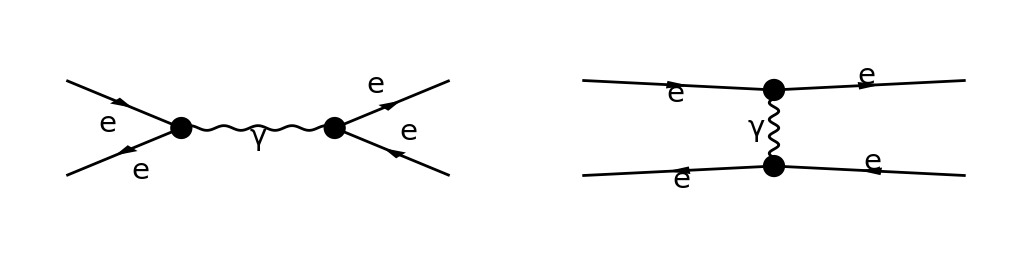

(e^2 (φ(OverBar[p_3],m_e)).(γ̄)^Lor1.(φ(OverBar[p_1],m_e)) (φ(-OverBar[p_2],m_e)).(γ̄)^Lor1.(φ(-OverBar[p_4],m_e)))/(OverBar[p_4]-OverBar[p_2])^2-(e^2 (φ(-OverBar[p_2],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_e)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_e)))/(OverBar[p_3]+OverBar[p_4])^2

(2 e^4 (8 m_e^4 (s^2+s t+t^2)-4 m_e^2 (s^3+s^2 (u-2 t)+s t (3 u-2 t)+t^2 (t+u))+s^4+s^2 u^2+2 s t u^2+t^4+t^2 u^2))/(s^2 t^2)

(2 e^4 (s^4+s^2 u^2+2 s t u^2+t^4+t^2 u^2))/(s^2 t^2)

```mathematica
(* QED: e- e+ -> e- e+ (Bhabha) *)
topology = CreateTopologies[0,2->2]; 
feynman1=InsertFields[topology, {F[2,{1}],-F[2,{1}]}->{F[2,{1}],-F[2,{1}]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman1, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude1[0]=FCFAConvert[CreateFeynAmp[feynman1],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_e"],SMP["m_e"],SMP["m_e"]];
squareamplitude1[0]=(amplitude1[0] (ComplexConjugate[amplitude1[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//Simplify
masslesssquareamplitude1[0] = squareamplitude1[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

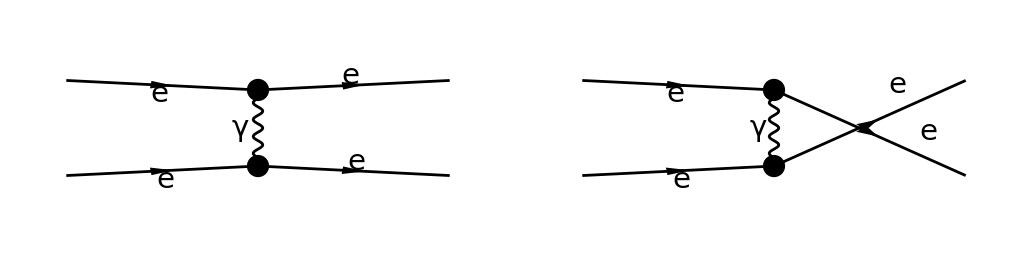

(e^2 (φ(OverBar[p_3],m_e)).(γ̄)^Lor1.(φ(OverBar[p_1],m_e)) (φ(-OverBar[p_2],m_e)).(γ̄)^Lor1.(φ(-OverBar[p_4],m_e)))/(OverBar[p_4]-OverBar[p_2])^2-(e^2 (φ(-OverBar[p_2],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_e)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_e)))/(OverBar[p_3]+OverBar[p_4])^2

(2 e^4 (8 m_e^4 (s^2+s t+t^2)-4 m_e^2 (s^3+s^2 (u-2 t)+s t (3 u-2 t)+t^2 (t+u))+s^4+s^2 u^2+2 s t u^2+t^4+t^2 u^2))/(s^2 t^2)

(2 e^4 (s^4+s^2 u^2+2 s t u^2+t^4+t^2 u^2))/(s^2 t^2)

```mathematica
(* QED: e- e- -> e- e- *)
topology = CreateTopologies[0,2->2]; 
feynman2=InsertFields[topology, {F[2,{1}],F[2,{1}]}->{F[2,{1}],F[2,{1}]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman2, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude2[0]=FCFAConvert[CreateFeynAmp[feynman1],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_e"],SMP["m_e"],SMP["m_e"]];
squareamplitude2[0]=(amplitude2[0] (ComplexConjugate[amplitude2[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//Simplify
masslesssquareamplitude2[0] = squareamplitude2[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

```mathematica
(* QED: e+ e+ -> e+ e+ *)
topology = CreateTopologies[0,2->2]; 
feynman3=InsertFields[topology, {F[2,{1}],F[2,{1}]}->{F[2,{1}],F[2,{1}]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman3, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude3[0]=FCFAConvert[CreateFeynAmp[feynman3],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_e"],SMP["m_e"],SMP["m_e"]];
squareamplitude3[0]=(amplitude3[0] (ComplexConjugate[amplitude3[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//Simplify
masslesssquareamplitude3[0] = squareamplitude3[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

-Graphics-

(e^2 (φ(OverBar[p_4],m_e)).(γ̄)^Lor1.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_e)).(γ̄)^Lor1.(φ(OverBar[p_2],m_e)))/(OverBar[p_3]-OverBar[p_2])^2-(e^2 (φ(OverBar[p_3],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_4],m_e)).(γ̄)^Lor2.(φ(OverBar[p_2],m_e)))/(OverBar[p_4]-OverBar[p_2])^2

(2 e^4 (-4 m_e^2 (s (t^2+3 t u+u^2)+t^3-2 t^2 u-2 t u^2+u^3)+8 m_e^4 (t^2+t u+u^2)+s^2 (t+u)^2+t^4+u^4))/(t^2 u^2)

(2 e^4 (s^2 (t+u)^2+t^4+u^4))/(t^2 u^2)

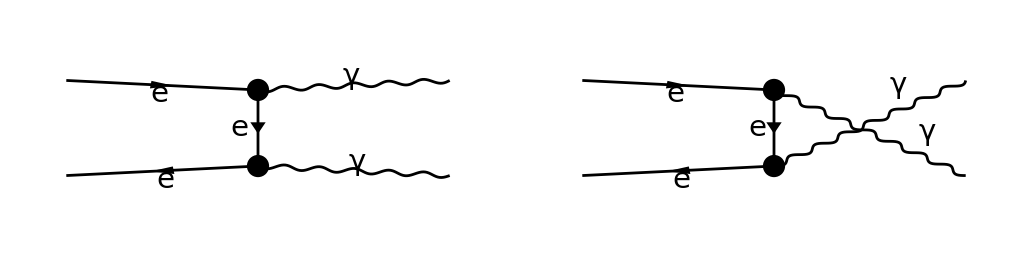

-(e^2 (φ(-OverBar[p_2],m_e)).(γ̄·(ε̄)^*(p_3)).(γ̄·(OverBar[p_3]-OverBar[p_2])+m_e).(γ̄·(ε̄)^*(p_4)).(φ(OverBar[p_1],m_e)))/((OverBar[p_2]-OverBar[p_3])^2-m_e^2)-(e^2 (φ(-OverBar[p_2],m_e)).(γ̄·(ε̄)^*(p_4)).(γ̄·(OverBar[p_4]-OverBar[p_2])+m_e).(γ̄·(ε̄)^*(p_3)).(φ(OverBar[p_1],m_e)))/((OverBar[p_2]-OverBar[p_4])^2-m_e^2)

(2 e^4 (m_e^4 (3 t^2+14 t u+3 u^2)-m_e^2 (t^3+7 t^2 u+7 t u^2+u^3)-6 m_e^8+t u (t^2+u^2)))/((t-m_e^2)^2 (u-m_e^2)^2)

(2 e^4 (t^2+u^2))/(t u)

```mathematica
(* QED: e- e+ -> photon photon (annihilation) *)
topology = CreateTopologies[0,2->2]; 
feynman4=InsertFields[topology, {F[2,{1}],-F[2,{1}]}->{V[1], V[1]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman4, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude4[0]=FCFAConvert[CreateFeynAmp[feynman4],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,TransversePolarizationVectors->{p3, p4}, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_e"],0, 0];
squareamplitude4[0]=(amplitude4[0] (ComplexConjugate[amplitude4[0]]))//FeynAmpDenominatorExplicit//DoPolarizationSums[#,p3,0]&//DoPolarizationSums[#,p4,0]&//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//TrickMandelstam[#,{s,t,u,2 SMP["m_e"]^2}]&//Simplify
masslesssquareamplitude4[0] = squareamplitude4[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

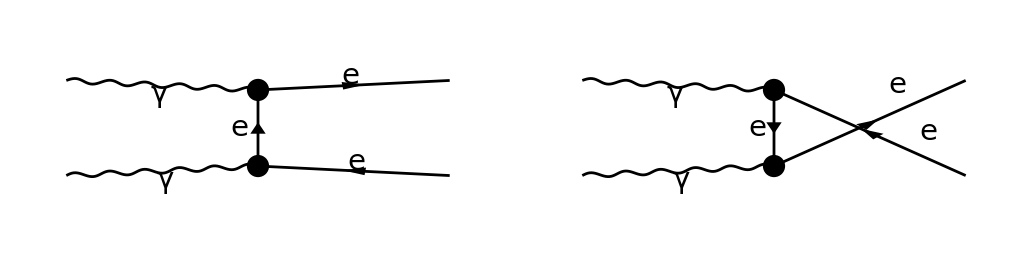

(e^2 (φ(OverBar[p_3],m_e)).(γ̄·ε̄(p_2)).(γ̄·(OverBar[p_3]-OverBar[p_2])+m_e).(γ̄·ε̄(p_1)).(φ(-OverBar[p_4],m_e)))/((OverBar[p_2]-OverBar[p_3])^2-m_e^2)+(e^2 (φ(OverBar[p_3],m_e)).(γ̄·ε̄(p_1)).(γ̄·(OverBar[p_2]-OverBar[p_4])+m_e).(γ̄·ε̄(p_2)).(φ(-OverBar[p_4],m_e)))/((OverBar[p_4]-OverBar[p_2])^2-m_e^2)

(2 e^4 (m_e^4 (3 t^2+14 t u+3 u^2)-m_e^2 (t^3+7 t^2 u+7 t u^2+u^3)-6 m_e^8+t u (t^2+u^2)))/((t-m_e^2)^2 (u-m_e^2)^2)

(2 e^4 (t^2+u^2))/(t u)

```mathematica
(* QED: photon photon -> e- e+ (pair creation)*)
topology = CreateTopologies[0,2->2]; 
feynman5=InsertFields[topology, {V[1], V[1]}->{F[2,{1}],-F[2,{1}]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman5, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude5[0]=FCFAConvert[CreateFeynAmp[feynman5],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,TransversePolarizationVectors->{p1, p2}, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,0, 0,SMP["m_e"],SMP["m_e"]];
squareamplitude5[0]=(amplitude5[0] (ComplexConjugate[amplitude5[0]]))//FeynAmpDenominatorExplicit//DoPolarizationSums[#,p1,0]&//DoPolarizationSums[#,p2,0]&//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//TrickMandelstam[#,{s,t,u,2 SMP["m_e"]^2}]&//Simplify
masslesssquareamplitude5[0] = squareamplitude5[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

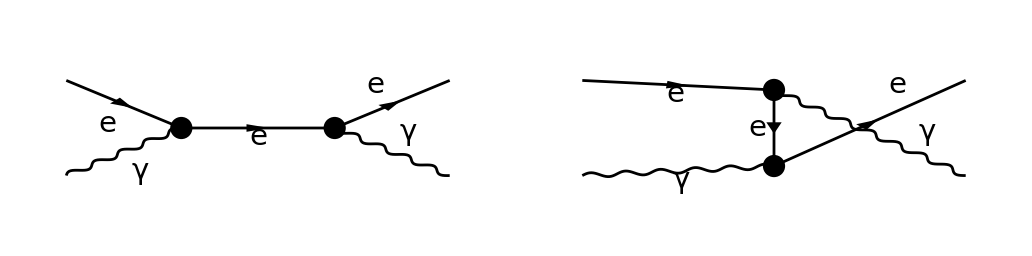

-(e^2 (φ(OverBar[p_3],m_e)).(γ̄·ε̄(p_2)).(γ̄·(OverBar[p_3]-OverBar[p_2])+m_e).(γ̄·(ε̄)^*(p_4)).(φ(OverBar[p_1],m_e)))/((OverBar[p_2]-OverBar[p_3])^2-m_e^2)-(e^2 (φ(OverBar[p_3],m_e)).(γ̄·(ε̄)^*(p_4)).(γ̄·(OverBar[p_3]+OverBar[p_4])+m_e).(γ̄·ε̄(p_2)).(φ(OverBar[p_1],m_e)))/((-OverBar[p_3]-OverBar[p_4])^2-m_e^2)

(2 e^4 (-m_e^4 (3 s^2+14 s u+3 u^2)+m_e^2 (s^3+7 s^2 u+7 s u^2+u^3)+6 m_e^8-s u (s^2+u^2)))/((s-m_e^2)^2 (u-m_e^2)^2)

-(2 e^4 (s^2+u^2))/(s u)

```mathematica
(* QED: e- photon -> e- photon (Compton)*)
topology = CreateTopologies[0,2->2]; 
feynman6=InsertFields[topology, {F[2,{1}],V[1]}->{F[2,{1}], V[1]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman6, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude6[0]=FCFAConvert[CreateFeynAmp[feynman6],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,TransversePolarizationVectors->{p2, p4}, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"], 0,SMP["m_e"], 0];
squareamplitude6[0]=(amplitude6[0] (ComplexConjugate[amplitude6[0]]))//FeynAmpDenominatorExplicit//DoPolarizationSums[#,p2,0]&//DoPolarizationSums[#,p4,0]&//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//TrickMandelstam[#,{s,t,u,2 SMP["m_e"]^2}]&//Simplify
masslesssquareamplitude6[0] = squareamplitude6[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

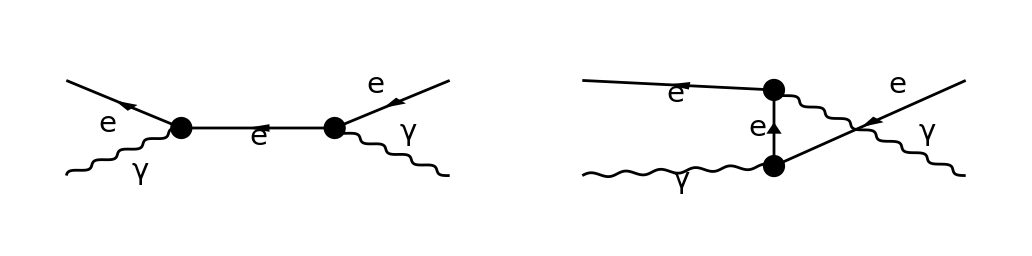

(e^2 (φ(-OverBar[p_1],m_e)).(γ̄·(ε̄)^*(p_4)).(γ̄·(OverBar[p_2]-OverBar[p_3])+m_e).(γ̄·ε̄(p_2)).(φ(-OverBar[p_3],m_e)))/((OverBar[p_3]-OverBar[p_2])^2-m_e^2)+(e^2 (φ(-OverBar[p_1],m_e)).(γ̄·ε̄(p_2)).(γ̄·(-OverBar[p_3]-OverBar[p_4])+m_e).(γ̄·(ε̄)^*(p_4)).(φ(-OverBar[p_3],m_e)))/((OverBar[p_3]+OverBar[p_4])^2-m_e^2)

(2 e^4 (-m_e^4 (3 s^2+14 s u+3 u^2)+m_e^2 (s^3+7 s^2 u+7 s u^2+u^3)+6 m_e^8-s u (s^2+u^2)))/((s-m_e^2)^2 (u-m_e^2)^2)

-(2 e^4 (s^2+u^2))/(s u)

```mathematica
(* QED: e+ photon -> e+ photon *)
topology = CreateTopologies[0,2->2]; 
feynman7=InsertFields[topology, {-F[2,{1}],V[1]}->{-F[2,{1}], V[1]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman7, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude7[0]=FCFAConvert[CreateFeynAmp[feynman7],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,TransversePolarizationVectors->{p2, p4}, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"], 0,SMP["m_e"], 0];
squareamplitude7[0]=(amplitude7[0] (ComplexConjugate[amplitude7[0]]))//FeynAmpDenominatorExplicit//DoPolarizationSums[#,p2,0]&//DoPolarizationSums[#,p4,0]&//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//TrickMandelstam[#,{s,t,u,2 SMP["m_e"]^2}]&//Simplify
masslesssquareamplitude7[0] = squareamplitude7[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

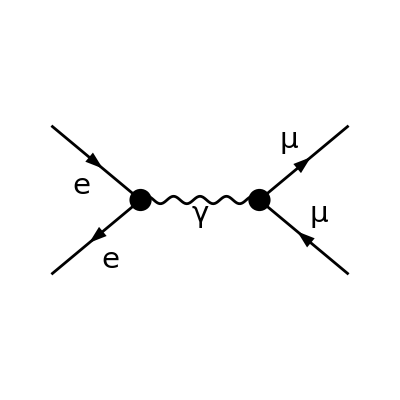

-(e^2 (φ(-OverBar[p_2],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_3],m_μ)).(γ̄)^Lor2.(φ(-OverBar[p_4],m_μ)))/(OverBar[p_3]+OverBar[p_4])^2

(2 e^4 (2 m_e^2 (2 m_μ^2+s-t-u)+2 m_e^4+2 m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

(2 e^4 (t^2+u^2))/s^2

```mathematica
(* QED: e- e+ -> mu- mu+ *)
topology = CreateTopologies[0,2->2]; 
feynman8=InsertFields[topology, {F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman8, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude8[0]=FCFAConvert[CreateFeynAmp[feynman8],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_e"],SMP["m_mu"],SMP["m_mu"]];
squareamplitude8[0]=(amplitude8[0] (ComplexConjugate[amplitude8[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//Simplify
masslesssquareamplitude8[0] = squareamplitude8[0]//ReplaceAll[#,{SMP["m_e"]->0,SMP["m_mu"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

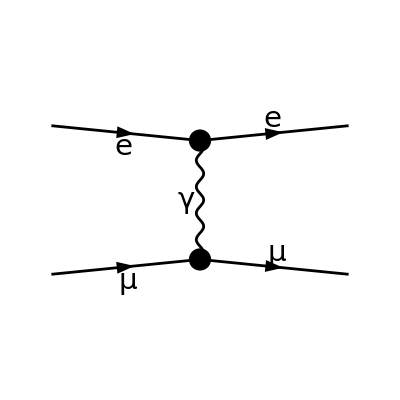

-(e^2 (φ(OverBar[p_3],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p_4],m_μ)).(γ̄)^Lor2.(φ(OverBar[p_2],m_μ)))/(OverBar[p_4]-OverBar[p_2])^2

(2 e^4 (-2 m_e^2 (-2 m_μ^2+s-t+u)+2 m_e^4+2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

(2 e^4 (s^2+u^2))/t^2

```mathematica
(* QED: e- mu- -> e- mu- *)
topology = CreateTopologies[0,2->2]; 
feynman9=InsertFields[topology, {F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]}, InsertionLevel->{Classes}, Restrictions -> QEDOnly];
Paint[feynman9, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude9[0]=FCFAConvert[CreateFeynAmp[feynman9],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];
squareamplitude9[0]=(amplitude9[0] (ComplexConjugate[amplitude9[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//Simplify
masslesssquareamplitude9[0] = squareamplitude9[0]//ReplaceAll[#,{SMP["m_e"]->0,SMP["m_mu"]->0}]&//Simplify
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

```mathematica
Print["\tCPU Time used: ",Round[N[TimeUsed[],4],0.001]," s."];
```

CPU Time used: 5.838 s.

```mathematica
FeynCalcHowToCite[]
```

• V. Shtabovenko, R. Mertig and F. Orellana, arXiv:2312.14089.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Null